# Rayleigh Quotient and Inverse Iteration

For the next few lectures A∈ℝ^(m×m) is symmetric A=Aᵀ.  This means that A is orthogonally diagonalizable with real eigenvalues i.e.
	A=Q.Λ.Qᵀ
with Q=(q_1 | | | q_2 | | | … | | | q_m) satisfying A.q_i=λ_i q_i with Λ=dia(λ_1,λ_2,…,λ_m).

## Rayleigh Quotient

Critical points v of the Rayleigh quotient
	r(x)=(x.A.x)/(x.x)
are eigenvectors of A with eigenvalues r(v).   This is immediate once you differentiate r(x)
	∇r(x).b=((b.A.x + x.A.b) (x.x)-(x.A.x)(x.b + b.x))/(x.x)^2=(2(x.A.b) (x.x) - 2(x.A.x)(x.b))/(x.x)^2
which gives
	∇r(x)=2 (x.x)^-2(A.x-r(x) x).
We can look at this in a projected contour plot in any dimension.

```mathematica
m=6; A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
r[A_,x_]:= x.A.x/(x.x)
V=Eigenvectors[A];
{u1,u2}=Map[Normalize,RandomReal[{-1,1},{2,m}]];
TabView[
Table[ContourPlot[r[A,V⟦i⟧+ϵ1 u1 +ϵ2 u2],{ϵ1,-0.5,0.5},{ϵ2,-0.5,0.5},
Contours->54,PlotPoints->50,Epilog->{Red,Point[{0,0}]}],
{i,m}]]
```

123456

```mathematica
r[A_List,x_List]:= x.A.x/(x.x)
m=3; A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
λs=Eigenvalues[A];
{λMin,λMax}={Min[λs],Max[λs]};
```

```mathematica
ParametricPlot
```

ParametricPlot

```mathematica
PolyhedronData[Sphere[{0,0,0},1]]
```

PolyhedronData::notdef: PolyhedronData has no value associated with the specified argument(s).

PolyhedronData[Sphere[{0,0,0},1]]

```mathematica
FullForm[Graphics3D[Sphere[{0,0,0},1]]]
```

Graphics3D[Sphere[List[0,0,0],1]]

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
V=Eigenvectors[A];
Pic=ParametricPlot3D[{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},{θ,0,2Pi},{ϕ,0, π},
ColorFunction->Function[{x,y,z,θ,ϕ},Hue[{x,y,z}.A.{x,y,z}]],PlotPoints->50];
TabView[{
Show[Pic,ViewPoint->3V⟦1⟧],
Show[Pic,ViewPoint->3V⟦2⟧],
Show[Pic,ViewPoint->3V⟦3⟧]}]
```

123

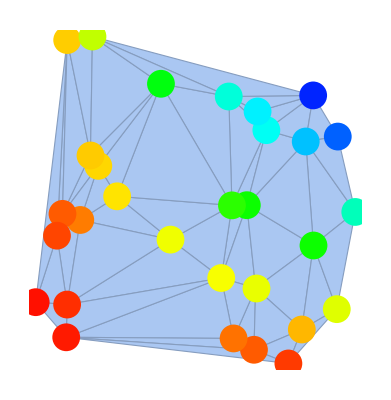
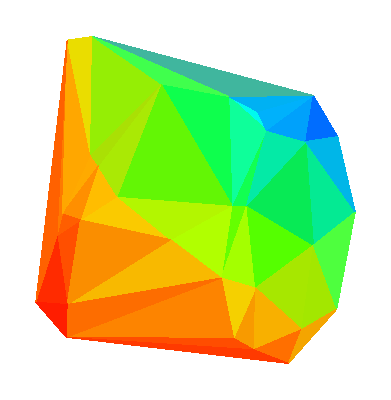

```mathematica
p=RandomReal[{0,1},{30,2}];
c=Map[Hue[Sin[#⟦1⟧ #⟦2⟧]]&,p];
R=DelaunayMesh[p];
{Show[DelaunayMesh[p],Graphics[Graphics[MapThread[{PointSize[.05],#1,Point[#2]}&,{c,p}]]]],
Graphics[GraphicsComplex[MeshCoordinates[R],MeshCells[R,2],VertexColors->c]]}
```

```mathematica
r[A_List,x_List]:= x.A.x/(x.x)
m=3; A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
{λs,V}=Eigensystem[A];
{λMin,λMax}={Min[λs],Max[λs]};
MyMesh =DiscretizeRegion[Sphere[{0,0,0},1]];
{pts,cells}={MeshCoordinates[MyMesh],MeshCells[MyMesh,2]};
colors =Map[Hue[0.9(#.A.#-λMin)/(λMax-λMin)]&,pts];
Pic=Graphics3D[{{PointSize[0.02],Point[V]},GraphicsComplex[pts,cells,VertexColors->colors]}];
TabView[{
1->Show[Pic, ViewPoint->2 V⟦1⟧],
2->Show[Pic, ViewPoint->2 V⟦2⟧],
3->Show[Pic, ViewPoint->2 V⟦3⟧],
-1->Show[Pic, ViewPoint->-2 V⟦1⟧],
-2->Show[Pic, ViewPoint->-2 V⟦2⟧],
-3->Show[Pic, ViewPoint->-2 V⟦3⟧]
}]
```

123456

## Power Iteration

Power iteration improves an approximation for the eigenvector associated with the largest eigenvalue repeatedly multiplying by the matrix and normalizing. It is pretty simple.  You can see the convergence of the eigenvector and the Rayleigh quotient!

### Script

```mathematica
m=6;A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
r[A_][x_]:=x.A.x 
λs=Eigenvalues[A]
MaxIter=44;
v0=Normalize[RandomReal[{-1,1},m]];
vData=NestList[Normalize[A.#]&,v0,MaxIter];
λData=Map[r[A],vData];
TabView[{
"vecs"->MatrixPlot[vData],
"vals"->ListPlot[λData,
FrameLabel->{"iter","λ"},GridLines->{Automatic,λs},PlotRange->All,Frame->True],
"rate"->ListLogPlot[Abs[λData-λs⟦1⟧],
FrameLabel->{"iter","err"},GridLines->Automatic,Frame->True]
}]
```

{3.47175,-3.07611,-2.56629,2.20546,-1.31986,0.274711}

123

## Inverse Power Iteration

Inverse Power iteration improves an approximation for the eigenvector associated with the “smallest” eigenvalue repeatedly multiplying by the inverse or the matrix and normalizing. It is pretty simple.  You can see the convergence of the eigenvector and the Rayleigh quotient!

### Script

```mathematica
m=6;A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
r[A_][x_]:=x.A.x 
λs=Eigenvalues[A]
MaxIter=34;
v0=Normalize[RandomReal[{-1,1},m]];
LinSol=LinearSolve[A];
vData=NestList[Normalize[LinSol[#]]&,v0,MaxIter];
λData=Map[r[A],vData];
TabView[{
"vecs"->MatrixPlot[vData],
"vals"->ListPlot[λData,
FrameLabel->{"iter","λ"},GridLines->{Automatic,λs},PlotRange->All,Frame->True],
"rate"->ListLogPlot[Abs[λData-λs⟦-1⟧],
FrameLabel->{"iter","err"},GridLines->Automatic,Frame->True]
}]
```

{2.94079,-1.82903,1.47442,-1.20183,-0.971437,0.486983}

123

## Shifted Inverse Power Iteration

Shifted Inverse Power iteration improves an approximation for the eigenvector associated with the eigen vaue near a target μ (called a shift) by repeatedly multiplying by (A- μ I)^-1and normalizing. It is pretty simple.  You can see the convergence of the eigenvector and the Rayleigh quotient!

### Script

```mathematica
m=6;A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
r[A_][x_]:=x.A.x 
λs=Eigenvalues[A]
```

{-2.84399,-2.27075,1.97872,-0.874327,0.825127,0.244246}

We need to pick a target!

```mathematica
μ=0.8;
MaxIter=34;
v0=Normalize[RandomReal[{-1,1},m]];
LinSol=LinearSolve[A-μ IdentityMatrix[m]];
vData=NestList[Normalize[LinSol[#]]&,v0,MaxIter];
λData=Map[r[A],vData];
TabView[{
"vecs"->MatrixPlot[vData],
"vals"->ListPlot[λData,
FrameLabel->{"iter","λ"},GridLines->{Automatic,λs},PlotRange->All,Frame->True],
"rate"->ListLogPlot[Abs[λData-λData⟦-1⟧],
FrameLabel->{"iter","err"},GridLines->Automatic,Frame->True]
}]
```

123

## Function

We need to decide when to stop our iteration.  The code

{-3.51701,3.40445,2.34527,-2.17453,1.42738,0.396472}

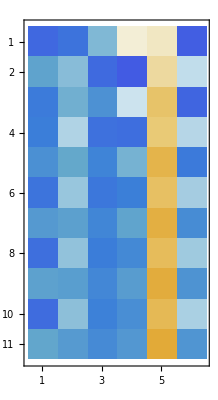

```mathematica
m=6;A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
Eigenvalues[A]
MaxIter=10;
v0=Normalize[RandomReal[{-1,1},m]];
vData=NestList[Normalize[A.#]&,v0,MaxIter];
MatrixPlot[vData]
```

## Inverse Iteration

## Rayleigh Quotient Iteration